## Bounds on EDGB Theory From the Overall Posterior of GW150914

```mathematica
dataOverall1=Import[NotebookDirectory[]<>"/overall_post.csv","CSV"];(*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
dataOverall2=Import[NotebookDirectory[]<>"/-1pn-phase-only-beta.csv","CSV"] (*PPE beta*)
dataOverall3=Import[NotebookDirectory[]<>"/-1pn-amp-only-alpha.csv","CSV"](*PPE alpha*)
```

{{8.35636×10^-6},{8.06129×10^-6},{7.78567×10^-6},{7.82844×10^-6},{7.95075×10^-6},{7.79311×10^-6},{8.77808×10^-6},{0.0000100423},52236,{8.24625×10^-6},{0.0000121047},{9.43185×10^-6},{0.0000142587},{8.36918×10^-6},{7.9195×10^-6},{7.90796×10^-6},{7.72341×10^-6}}
 |  |  |  |

{{0.0101774},{0.0103138},{0.0101751},{0.0102443},{0.0102805},{0.0101639},{0.0101491},{0.0100966},{0.0101554},52234,{0.0102537},{0.0101734},{0.0100435},{0.0101434},{0.0100688},{0.0102518},{0.0102583},{0.0102284},{0.0102054}}
 |  |  |  |

```mathematica
0.000085792380799407//ScientificForm
```

8.57924×10^-5

```mathematica
5.72*10^-4*3*10^5
```

171.6

```mathematica
dataOverall4=Import[NotebookDirectory[]<>"/-1pn-combined-correlated-beta.csv","CSV"]; (*PPE beta for phase and amp combined*)
```

```mathematica
χ1All=dataOverall1[[All,7]]
 (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]]
```

{0.474815,0.967842,0.407971,0.3213,0.524324,0.12256,0.599379,0.588323,0.389913,0.542379,0.366422,0.551819,0.410831,0.481296,52224,0.983049,0.382938,0.51136,0.350405,0.50589,0.748399,0.705519,0.565014,0.778983,0.812994,0.778319,0.0806167,0.719679,0.303922}
 |  |  |  |

{0.0924668,0.949848,0.658073,0.69925,0.52498,0.451105,0.111901,0.955939,0.541919,0.306143,0.746212,0.869911,0.287751,0.478399,52224,0.226841,0.852167,0.174555,0.665992,0.0495768,0.948692,0.398673,0.940458,0.850016,0.163463,0.724908,0.633309,0.111302,0.287212}
 |  |  |  |

```mathematica
DL=dataOverall1[[All,2]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{2.52079×10^16,4.85528×10^16,6.35231×10^16,5.24927×10^16,3.73515×10^16,3.05455×10^16,4.78442×10^16,3.9636×10^16,52236,5.03767×10^16,3.80794×10^16,5.61282×10^16,5.43259×10^16,5.42488×10^16,3.54656×10^16,4.06701×10^16,3.20266×10^16}
 |  |  |  |

```mathematica
Clear[z]
```

```mathematica
Clear[z1,z2]
```

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.054871,0.102135,0.130944,0.109823,0.0798379,0.0659518,0.100744,0.0844401,0.111302,52234,0.0613878,0.105704,0.0813074,0.116848,0.113374,0.113224,0.0760166,0.086514,0.0689964}
 |  |  |  |

```mathematica
m1All=dataOverall1[[All,5]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6 (*Ligo posterior gives mass in detector frame*)
m2All=dataOverall1[[All,6]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6
```

{0.0000737423,0.000052406,0.0000629487,0.0000589476,0.0000533338,0.0000668695,0.0000729009,0.0000812561,52237,0.0000934506,0.0000740165,0.000124027,0.0000656178,0.0000560597,0.0000650154,0.0000619624}
 |  |  |  |

{0.0000381435,0.0000473271,0.0000378045,0.0000415688,0.0000478977,0.0000395864,0.0000351205,0.0000329017,52237,0.0000292622,0.0000331739,0.0000224433,0.0000371517,0.0000460789,0.0000400992,0.0000423245}
 |  |  |  |

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=dataOverall2[[All,1]](*1-sigma upper bound*)
αppEAll=dataOverall3[[All,1]](*1-sigma upper bound*)
```

{8.35636×10^-6,8.06129×10^-6,7.78567×10^-6,7.82844×10^-6,7.95075×10^-6,7.79311×10^-6,8.77808×10^-6,0.0000100423,8.80668×10^-6,52235,8.24625×10^-6,0.0000121047,9.43185×10^-6,0.0000142587,8.36918×10^-6,7.9195×10^-6,7.90796×10^-6,7.72341×10^-6}
 |  |  |  |

{0.0101774,0.0103138,0.0101751,0.0102443,0.0102805,0.0101639,0.0101491,0.0100966,0.0101554,0.0101637,52232,0.0102249,0.0102537,0.0101734,0.0100435,0.0101434,0.0100688,0.0102518,0.0102583,0.0102284,0.0102054}
 |  |  |  |

```mathematica
βppEComb=dataOverall4[[All,1]]
```

{8.34759×10^-6,8.06461×10^-6,7.78128×10^-6,7.8275×10^-6,7.9539×10^-6,7.78933×10^-6,8.76817×10^-6,0.0000100333,8.79687×10^-6,52235,8.23797×10^-6,0.000012109,9.42184×10^-6,0.0000142818,8.36075×10^-6,7.92229×10^-6,7.90293×10^-6,7.72214×10^-6}
 |  |  |  |

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
s2All=2/χ2All^2*(√(1-χ2All^2)-1+χ2All^2)
```

{0.997853,0.476435,0.859069,0.833736,0.91957,0.94318,0.99685,0.453885,0.913298,52234,0.480475,0.956754,0.507364,0.690034,0.993229,0.81576,0.87254,0.996884,0.97848}
 |  |  |  |

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] (*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*)
```

{0.00052641,0.0462628,0.00149135,0.00472275,0.0315292,0.00108299,0.000412798,0.00198254,52236,0.000594841,0.000633253,0.000802846,0.0000271555,0.00113981,0.0209629,0.00091143,0.00193841}
 |  |  |  |

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll](*Sigma_Zeta from amplitude corrections*)
```

{0.0171731,1.58544,0.0522067,0.165541,1.092,0.0378336,0.0127841,0.053391,0.0167173,52234,5.77685,0.0196568,0.0140738,0.0231271,0.00051364,0.0373982,0.727332,0.0315769,0.0686073}
 |  |  |  |

```mathematica
ζcombAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEComb]
```

{0.000525858,0.0462819,0.00149051,0.00472218,0.0315417,0.00108247,0.000412332,0.00198078,52236,0.000594243,0.00063348,0.000801993,0.0000271994,0.00113866,0.0209703,0.00091085,0.00193809}
 |  |  |  |

```mathematica
Length[m1All]
```

52252

```mathematica
Length[βppEAll]
```

52252

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

51355

```mathematica
Length[ζAllampSelected]
```

46872

```mathematica
Mean[ζAllphaseSelected]
```

0.0173906

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.0747384

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.00052641},52250,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193841}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.00052641,0.0171763},52250,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193841,0.0686092}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] ;(*Data satisfying zeta_phase<1*)
```

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.00052641,0.0171763},46870,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193841,0.0686092}}
 |  |  |  |

```mathematica
A4[[All,12]];
```

```mathematica
Length[A3]
```

51355

```mathematica
Length[A4]
```

46872

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.094265

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5;(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{1.90946,5.21136,2.23079,2.96886,4.80615,2.17585,1.7348,2.71403,1.84069,52234,7.50751,1.8565,2.19325,2.03291,1.19129,2.12753,4.37881,2.05777,2.46544}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBphase]
```

3.02701

```mathematica
StandardDeviation[SqrtαEDGBphase]
```

6.01882

```mathematica
SqrtαEDGBcomb=((ζcombAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{1.90896,5.2119,2.23047,2.96877,4.80663,2.17559,1.73431,2.71343,1.84018,52234,7.50763,1.85603,2.19345,2.03237,1.19177,2.127,4.3792,2.05745,2.46534}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

7.19566

```mathematica
Mean[SqrtαEDGBphase]
```

3.02701

(α^2)_EDGB from phase correction:

```mathematica
LogSquaredαPhase=Log[SqrtαEDGBphase^4] (*This is Log of sigma_(alpha^2)*)
```

{2.58727,6.60336,3.20942,4.35271,6.27959,3.10969,2.20356,3.99374,2.44056,52234,8.06361,2.47476,3.14154,2.83787,0.700142,3.01985,5.90711,2.8865,3.60949}
 |  |  |  |

```mathematica
MaxLogSquaredαPhase=Max[LogSquaredαPhase]
```

25.6805

```mathematica
MinLogSquaredαPhase=Min[LogSquaredαPhase]
```

-0.475576

```mathematica
(*𝒟logα=HistogramDistribution[LogSquaredαPhase] ;*)
```

```mathematica
(*pslogαPhase=PDF[𝒟logα,x];*)
```

```mathematica
Histogram[LogSquaredαPhase];
```

```mathematica
(*fun1αphase[x_,y_]=1/(√(2*π)*Exp[y]/1.64485)*Exp[-x^2/(2*Exp[2*y]/1.64485^2)] *)
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2*Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLog=Prepend[10^Range[-7,12.5,0.1],0](*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

{0,1.×10^-7,1.25893×10^-7,1.58489×10^-7,1.99526×10^-7,2.51189×10^-7,3.16228×10^-7,3.98107×10^-7,5.01187×10^-7,6.30957×10^-7,7.94328×10^-7,1.×10^-6,1.25893×10^-6,1.58489×10^-6,1.99526×10^-6,2.51189×10^-6,3.16228×10^-6,3.98107×10^-6,5.01187×10^-6,6.30957×10^-6,7.94328×10^-6,0.00001,0.0000125893,0.0000158489,0.0000199526,0.0000251189,0.0000316228,0.0000398107,0.0000501187,0.0000630957,0.0000794328,0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228,398.107,501.187,630.957,794.328,1000.,1258.93,1584.89,1995.26,2511.89,3162.28,3981.07,5011.87,6309.57,7943.28,10000.,12589.3,15848.9,19952.6,25118.9,31622.8,39810.7,50118.7,63095.7,79432.8,100000.,125893.,158489.,199526.,251189.,316228.,398107.,501187.,630957.,794328.,1.×10^6,1.25893×10^6,1.58489×10^6,1.99526×10^6,2.51189×10^6,3.16228×10^6,3.98107×10^6,5.01187×10^6,6.30957×10^6,7.94328×10^6,1.×10^7,1.25893×10^7,1.58489×10^7,1.99526×10^7,2.51189×10^7,3.16228×10^7,3.98107×10^7,5.01187×10^7,6.30957×10^7,7.94328×10^7,1.×10^8,1.25893×10^8,1.58489×10^8,1.99526×10^8,2.51189×10^8,3.16228×10^8,3.98107×10^8,5.01187×10^8,6.30957×10^8,7.94328×10^8,1.×10^9,1.25893×10^9,1.58489×10^9,1.99526×10^9,2.51189×10^9,3.16228×10^9,3.98107×10^9,5.01187×10^9,6.30957×10^9,7.94328×10^9,1.×10^10,1.25893×10^10,1.58489×10^10,1.99526×10^10,2.51189×10^10,3.16228×10^10,3.98107×10^10,5.01187×10^10,6.30957×10^10,7.94328×10^10,1.×10^11,1.25893×10^11,1.58489×10^11,1.99526×10^11,2.51189×10^11,3.16228×10^11,3.98107×10^11,5.01187×10^11,6.30957×10^11,7.94328×10^11,1.×10^12,1.25893×10^12,1.58489×10^12,1.99526×10^12,2.51189×10^12,3.16228×10^12}

```mathematica
fun1αphaseTable[y_]=Table[{αSampleLog[[i]],fun1αphase[αSampleLog[[i]],y]},{i,1,Length[αSampleLog]}];(*Table for fun1αphase*)
```

```mathematica
(*αPhaseMC[x_]=pslogαPhase*)
```

```mathematica
(*αPhaseMC[5]*)
```

```mathematica
(*αPhaseMC[33]*)
```

```mathematica
(*αMCSample=Range[5,37,1.1];*)
```

```mathematica
(*αMCTable=Table[{αMCSample[[i]],αPhaseMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];*)
```

```mathematica
(*αMCTableInterp=Interpolation[αMCTable];*)
```

```mathematica
(*plotαMCTableInterp=Plot[αMCTableInterp[x],{x,5,37},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]*)
```

```mathematica
(*plot5=Plot[αPhaseMC[x],{x,5,37},Filling->Axis,PlotStyle->Gray,PlotRange->All]*)
```

```mathematica
(*Show[plot5,plotαMCTableInterp] (*Interpolation matches the actual pdf of monte-carlo*)*)
```

```mathematica
𝒟logαSq=SmoothKernelDistribution[LogSquaredαPhase]
```

DataDistribution[…]

```mathematica
𝒟logαSq2=PDF[𝒟logαSq,x]
```

Piecewise[{{InterpolatingFunction[…][x], -1.33387≤x≤26.5388}, {0, True}}]

```mathematica
𝒟logαSq3[x_]=𝒟logαSq2
```

Piecewise[{{InterpolatingFunction[…][x], -1.33387≤x≤26.5388}, {0, True}}]

```mathematica
αFinalPDFPhaseLog=Table[{fun1αphaseTable[y][[i,1]],NIntegrate[fun1αphaseTable[y][[i,2]]𝒟logαSq3[y],{y,MinLogSquaredαPhase,MaxLogSquaredαPhase}]},{i,1,Length[fun1αphaseTable[y]]}]
```

{{0,0.0331875},{1.×10^-7,0.0331875},{1.25893×10^-7,0.0331875},{1.58489×10^-7,0.0331875},{1.99526×10^-7,0.0331875},{2.51189×10^-7,0.0331875},{3.16228×10^-7,0.0331875},{3.98107×10^-7,0.0331875},{5.01187×10^-7,0.0331875},{6.30957×10^-7,0.0331875},{7.94328×10^-7,0.0331875},{1.×10^-6,0.0331875},{1.25893×10^-6,0.0331875},{1.58489×10^-6,0.0331875},{1.99526×10^-6,0.0331875},{2.51189×10^-6,0.0331875},{3.16228×10^-6,0.0331875},{3.98107×10^-6,0.0331875},{5.01187×10^-6,0.0331875},{6.30957×10^-6,0.0331875},{7.94328×10^-6,0.0331875},{0.00001,0.0331875},{0.0000125893,0.0331875},{0.0000158489,0.0331875},{0.0000199526,0.0331875},{0.0000251189,0.0331875},{0.0000316228,0.0331875},{0.0000398107,0.0331875},{0.0000501187,0.0331875},{0.0000630957,0.0331875},{0.0000794328,0.0331875},{0.0001,0.0331875},{0.000125893,0.0331875},{0.000158489,0.0331875},{0.000199526,0.0331875},{0.000251189,0.0331875},{0.000316228,0.0331875},{0.000398107,0.0331875},{0.000501187,0.0331875},{0.000630957,0.0331875},{0.000794328,0.0331875},{0.001,0.0331875},{0.00125893,0.0331875},{0.00158489,0.0331875},{0.00199526,0.0331875},{0.00251189,0.0331875},{0.00316228,0.0331875},{0.00398107,0.0331874},{0.00501187,0.0331874},{0.00630957,0.0331874},{0.00794328,0.0331874},{0.01,0.0331873},{0.0125893,0.0331872},{0.0158489,0.033187},{0.0199526,0.0331868},{0.0251189,0.0331863},{0.0316228,0.0331857},{0.0398107,0.0331846},{0.0501187,0.033183},{0.0630957,0.0331803},{0.0794328,0.0331762},{0.1,0.0331695},{0.125893,0.0331591},{0.158489,0.0331426},{0.199526,0.0331165},{0.251189,0.0330754},{0.316228,0.0330109},{0.398107,0.0329102},{0.501187,0.0327545},{0.630957,0.0325166},{0.794328,0.0321601},{1.,0.0316398},{1.25893,0.0309066},{1.58489,0.0299147},{1.99526,0.0286283},{2.51189,0.0270205},{3.16228,0.0250724},{3.98107,0.0227822},{5.01187,0.0201836},{6.30957,0.0173624},{7.94328,0.0144537},{10.,0.0116239},{12.5893,0.00903932},{15.8489,0.00682705},{19.9526,0.00504356},{25.1189,0.00367208},{31.6228,0.00264996},{39.8107,0.00190151},{50.1187,0.00135813},{63.0957,0.000965517},{79.4328,0.00068333},{100.,0.000481705},{125.893,0.00033842},{158.489,0.000237239},{199.526,0.00016637},{251.189,0.000117035},{316.228,0.0000826709},{398.107,0.0000585888},{501.187,0.0000416002},{630.957,0.0000295542},{794.328,0.0000209817},{1000.,0.0000148758},{1258.93,0.0000105389},{1584.89,7.47072×10^-6},{1995.26,5.29924×10^-6},{2511.89,3.75595×10^-6},{3162.28,2.65841×10^-6},{3981.07,1.8804×10^-6},{5011.87,1.32907×10^-6},{6309.57,9.37056×10^-7},{7943.28,6.58133×10^-7},{10000.,4.60742×10^-7},{12589.3,3.22258×10^-7},{15848.9,2.25746×10^-7},{19952.6,1.58507×10^-7},{25118.9,1.11541×10^-7},{31622.8,7.86709×10^-8},{39810.7,5.55238×10^-8},{50118.7,3.90996×10^-8},{63095.7,2.74937×10^-8},{79432.8,1.94059×10^-8},{100000.,1.38076×10^-8},{125893.,9.90393×10^-9},{158489.,7.15519×10^-9},{199526.,5.20774×10^-9},{251189.,3.81186×10^-9},{316228.,2.79396×10^-9},{398107.,2.03993×10^-9},{501187.,1.47425×10^-9},{630957.,1.04874×10^-9},{794328.,7.33046×10^-10},{1.×10^6,5.04699×10^-10},{1.25893×10^6,3.43801×10^-10},{1.58489×10^6,2.32841×10^-10},{1.99526×10^6,1.57618×10^-10},{2.51189×10^6,1.07121×10^-10},{3.16228×10^6,7.34488×10^-11},{3.98107×10^6,5.15146×10^-11},{5.01187×10^6,3.76445×10^-11},{6.30957×10^6,2.86524×10^-11},{7.94328×10^6,2.22243×10^-11},{1.×10^7,1.71708×10^-11},{1.25893×10^7,1.30047×10^-11},{1.58489×10^7,9.53106×10^-12},{1.99526×10^7,6.70353×10^-12},{2.51189×10^7,4.53164×10^-12},{3.16228×10^7,2.99295×10^-12},{3.98107×10^7,1.99272×10^-12},{5.01187×10^7,1.37363×10^-12},{6.30957×10^7,9.78026×10^-13},{7.94328×10^7,7.07246×10^-13},{1.×10^8,5.17415×10^-13},{1.25893×10^8,3.83872×10^-13},{1.58489×10^8,2.86656×10^-13},{1.99526×10^8,2.11663×10^-13},{2.51189×10^8,1.52546×10^-13},{3.16228×10^8,1.08318×10^-13},{3.98107×10^8,7.78225×10^-14},{5.01187×10^8,5.76314×10^-14},{6.30957×10^8,4.40221×10^-14},{7.94328×10^8,3.43268×10^-14},{1.×10^9,2.67004×10^-14},{1.25893×10^9,2.01276×10^-14},{1.58489×10^9,1.45097×10^-14},{1.99526×10^9,1.01564×10^-14},{2.51189×10^9,7.07879×10^-15},{3.16228×10^9,4.90612×10^-15},{3.98107×10^9,3.31081×10^-15},{5.01187×10^9,2.18008×10^-15},{6.30957×10^9,1.4643×10^-15},{7.94328×10^9,1.05968×10^-15},{1.×10^10,8.43798×10^-16},{1.25893×10^10,7.24017×10^-16},{1.58489×10^10,6.33723×10^-16},{1.99526×10^10,5.35864×10^-16},{2.51189×10^10,4.24135×10^-16},{3.16228×10^10,3.10574×10^-16},{3.98107×10^10,2.13242×10^-16},{5.01187×10^10,1.44482×10^-16},{6.30957×10^10,1.03902×10^-16},{7.94328×10^10,8.15764×10^-17},{1.×10^11,6.6149×10^-17},{1.25893×10^11,5.08092×10^-17},{1.58489×10^11,3.4406×10^-17},{1.99526×10^11,1.91917×10^-17},{2.51189×10^11,8.09554×10^-18},{3.16228×10^11,2.28918×10^-18},{3.98107×10^11,3.61357×10^-19},{5.01187×10^11,2.37232×10^-20},{6.30957×10^11,4.00617×10^-22},{7.94328×10^11,8.01375×10^-25},{1.×10^12,5.50602×10^-29},{1.25893×10^12,1.81718×10^-35},{1.58489×10^12,1.27135×10^-45},{1.99526×10^12,1.33959×10^-61},{2.51189×10^12,8.36099×10^-87},{3.16228×10^12,1.23885×10^-126}}

```mathematica
(*Export[NotebookDirectory[]<>"cdf.dat",αFinalPDFPhaseLog]*)
```

```mathematica
αFinalPDFPhaseInterpLog=Interpolation[αFinalPDFPhaseLog]
```

InterpolatingFunction[…]

```mathematica
αNormalization=NIntegrate[αFinalPDFPhaseInterpLog[x],{x,0,3.16*10^12}]
```

0.499439

```mathematica
αFinalPDFPhaseLogNorm=Table[{αFinalPDFPhaseLog[[i,1]],αFinalPDFPhaseLog[[i,2]]/αNormalization},{i,1,Length[αFinalPDFPhaseLog]}];
```

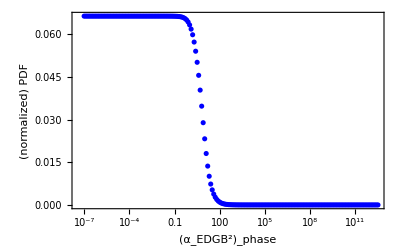

```mathematica
plotαFinalPDFPhaseLogNorm=ListLogLinearPlot[{αFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFPhaseInterpLogNorm=Interpolation[αFinalPDFPhaseLogNorm]
```

InterpolatingFunction[…]

```mathematica
αFinalCDFPhaseNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFPhaseInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}];
```

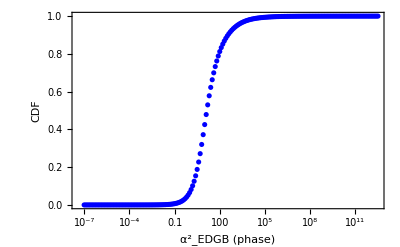

```mathematica
ListLogLinearPlot[αFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (phase)","CDF"}]
```

```mathematica
αFinalCDFPhaseNormInterp=Interpolation[αFinalCDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
αSquared90CLphase=x/.FindRoot[αFinalCDFPhaseNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

348.065

```mathematica
√√αSquared90CLphase//N   (*90% CL upper bound*)
```

4.31932

```mathematica
Subscript[α^2, EDGB] from amplitude correction:
```

```mathematica
LogSquaredαamp=Log[SqrtαEDGBamp^4]
```

{6.07248,10.1381,6.76496,7.90959,9.82486,6.66321,5.63673,7.28702,5.87111,5.90133,52233,11.6216,5.97281,6.2432,6.19856,3.64171,6.51077,9.45411,6.43167,7.17605}
 |  |  |  |

```mathematica
MaxLogSquaredαamp=Max[LogSquaredαamp]
```

29.2372

```mathematica
MinLogSquaredαamp=Min[LogSquaredαamp]
```

2.30312

```mathematica
𝒟logαamp=SmoothKernelDistribution[LogSquaredαamp]
```

DataDistribution[…]

```mathematica
𝒟logαamp2=PDF[𝒟logαamp,x]
```

Piecewise[{{InterpolatingFunction[…][x], 1.35757≤x≤30.1827}, {0, True}}]

```mathematica
𝒟logαamp3[x_]=𝒟logαamp2
```

Piecewise[{{InterpolatingFunction[…][x], 1.35757≤x≤30.1827}, {0, True}}]

```mathematica
(*𝒟logαamp=HistogramDistribution[LogSquaredαamp] ;*)
```

```mathematica
(*pslogαamp=PDF[𝒟logαamp,x];*)
```

```mathematica
(*Histogram[LogSquaredαamp];*)
```

```mathematica
(*αampMC[x_]=pslogαamp;*)
```

```mathematica
(*αampMC[35]*)
```

```mathematica
(*αampMC[5]*)
```

```mathematica
(*αMCSampleamp=Range[5,35,1.2];*)
```

```mathematica
(*αMCTableamp=Table[{αMCSampleamp[[i]],αampMC[αMCSampleamp[[i]]]},{i,1,Length[αMCSampleamp]}];*)
```

```mathematica
(*αMCTableInterpamp=Interpolation[αMCTableamp];*)
```

```mathematica
(*plotαMCTableInterpamp=Plot[αMCTableInterpamp[x],{x,9,34},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]*)
```

```mathematica
(*plot6=Plot[αampMC[x],{x,9,34},Filling->Axis,PlotStyle->Gray,PlotRange->All]*)
```

```mathematica
(*Show[plot6,plotαMCTableInterpamp]*)
```

```mathematica
αSampleLogamp=Prepend[10^Range[-7,12.7,0.1],0];
```

```mathematica
fun1αamp[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])];
```

```mathematica
fun1αampTable[y_]=Table[{αSampleLogamp[[i]],fun1αphase[αSampleLogamp[[i]],y]},{i,1,Length[αSampleLogamp]}];
```

```mathematica
αFinalPDFampLog=Table[{fun1αampTable[y][[i,1]],NIntegrate[fun1αampTable[y][[i,2]]*𝒟logαamp3[y],{y,MinLogSquaredαamp,MaxLogSquaredαPhase}]},{i,1,Length[fun1αampTable[y]]}]
```

{{0,0.0014119},{1.×10^-7,0.0014119},{1.25893×10^-7,0.0014119},{1.58489×10^-7,0.0014119},{1.99526×10^-7,0.0014119},{2.51189×10^-7,0.0014119},{3.16228×10^-7,0.0014119},{3.98107×10^-7,0.0014119},{5.01187×10^-7,0.0014119},{6.30957×10^-7,0.0014119},{7.94328×10^-7,0.0014119},{1.×10^-6,0.0014119},{1.25893×10^-6,0.0014119},{1.58489×10^-6,0.0014119},{1.99526×10^-6,0.0014119},{2.51189×10^-6,0.0014119},{3.16228×10^-6,0.0014119},{3.98107×10^-6,0.0014119},{5.01187×10^-6,0.0014119},{6.30957×10^-6,0.0014119},{7.94328×10^-6,0.0014119},{0.00001,0.0014119},{0.0000125893,0.0014119},{0.0000158489,0.0014119},{0.0000199526,0.0014119},{0.0000251189,0.0014119},{0.0000316228,0.0014119},{0.0000398107,0.0014119},{0.0000501187,0.0014119},{0.0000630957,0.0014119},{0.0000794328,0.0014119},{0.0001,0.0014119},{0.000125893,0.0014119},{0.000158489,0.0014119},{0.000199526,0.0014119},{0.000251189,0.0014119},{0.000316228,0.0014119},{0.000398107,0.0014119},{0.000501187,0.0014119},{0.000630957,0.0014119},{0.000794328,0.0014119},{0.001,0.0014119},{0.00125893,0.0014119},{0.00158489,0.0014119},{0.00199526,0.0014119},{0.00251189,0.0014119},{0.00316228,0.0014119},{0.00398107,0.0014119},{0.00501187,0.0014119},{0.00630957,0.0014119},{0.00794328,0.0014119},{0.01,0.0014119},{0.0125893,0.0014119},{0.0158489,0.0014119},{0.0199526,0.0014119},{0.0251189,0.0014119},{0.0316228,0.0014119},{0.0398107,0.0014119},{0.0501187,0.0014119},{0.0630957,0.0014119},{0.0794328,0.0014119},{0.1,0.00141189},{0.125893,0.00141189},{0.158489,0.00141189},{0.199526,0.00141189},{0.251189,0.00141188},{0.316228,0.00141187},{0.398107,0.00141185},{0.501187,0.00141182},{0.630957,0.00141178},{0.794328,0.00141171},{1.,0.0014116},{1.25893,0.00141142},{1.58489,0.00141115},{1.99526,0.00141071},{2.51189,0.00141002},{3.16228,0.00140893},{3.98107,0.00140722},{5.01187,0.00140453},{6.30957,0.00140034},{7.94328,0.00139387},{10.,0.001384},{12.5893,0.00136928},{15.8489,0.00134793},{19.9526,0.00131812},{25.1189,0.00127833},{31.6228,0.00122764},{39.8107,0.00116558},{50.1187,0.0010919},{63.0957,0.00100667},{79.4328,0.000910922},{100.,0.000807258},{125.893,0.000699821},{158.489,0.000593394},{199.526,0.00049237},{251.189,0.000400158},{316.228,0.000318985},{398.107,0.000249852},{501.187,0.000192626},{630.957,0.000146364},{794.328,0.00010973},{1000.,0.0000812721},{1258.93,0.000059552},{1584.89,0.0000432209},{1995.26,0.0000310963},{2511.89,0.0000222023},{3162.28,0.0000157506},{3981.07,0.0000111145},{5011.87,7.81276×10^-6},{6309.57,5.48423×10^-6},{7943.28,3.85591×10^-6},{10000.,2.72058×10^-6},{12589.3,1.92623×10^-6},{15848.9,1.36711×10^-6},{19952.6,9.71416×10^-7},{25118.9,6.90112×10^-7},{31622.8,4.89649×10^-7},{39810.7,3.46991×10^-7},{50118.7,2.45899×10^-7},{63095.7,1.744×10^-7},{79432.8,1.23671×10^-7},{100000.,8.75799×10^-8},{125893.,6.19538×10^-8},{158489.,4.37942×10^-8},{199526.,3.09005×10^-8},{251189.,2.17301×10^-8},{316228.,1.52298×10^-8},{398107.,1.06566×10^-8},{501187.,7.46204×10^-9},{630957.,5.23585×10^-9},{794328.,3.68164×10^-9},{1.×10^6,2.5943×10^-9},{1.25893×10^6,1.83028×10^-9},{1.58489×10^6,1.2895×10^-9},{1.99526×10^6,9.06737×10^-10},{2.51189×10^6,6.38849×10^-10},{3.16228×10^6,4.5317×10^-10},{3.98107×10^6,3.24062×10^-10},{5.01187×10^6,2.33423×10^-10},{6.30957×10^6,1.69396×10^-10},{7.94328×10^6,1.23793×10^-10},{1.×10^7,9.07868×10^-11},{1.25893×10^7,6.64585×10^-11},{1.58489×10^7,4.82597×10^-11},{1.99526×10^7,3.45585×10^-11},{2.51189×10^7,2.4326×10^-11},{3.16228×10^7,1.68449×10^-11},{3.98107×10^7,1.15176×10^-11},{5.01187×10^7,7.81388×10^-12},{6.30957×10^7,5.28728×10^-12},{7.94328×10^7,3.58401×10^-12},{1.×10^8,2.44426×10^-12},{1.25893×10^8,1.69561×10^-12},{1.58489×10^8,1.21911×10^-12},{1.99526×10^8,9.15522×10^-13},{2.51189×10^8,7.07006×10^-13},{3.16228×10^8,5.48158×10^-13},{3.98107×10^8,4.18916×10^-13},{5.01187×10^8,3.11116×10^-13},{6.30957×10^8,2.22123×10^-13},{7.94328×10^8,1.52039×10^-13},{1.×10^9,1.00878×10^-13},{1.25893×10^9,6.67142×10^-14},{1.58489×10^9,4.53954×10^-14},{1.99526×10^9,3.20409×10^-14},{2.51189×10^9,2.30967×10^-14},{3.16228×10^9,1.68299×10^-14},{3.98107×10^9,1.2412×10^-14},{5.01187×10^9,9.24048×10^-15},{6.30957×10^9,6.8487×10^-15},{7.94328×10^9,4.96954×10^-15},{1.×10^10,3.52676×10^-15},{1.25893×10^10,2.49955×10^-15},{1.58489×10^10,1.81341×10^-15},{1.99526×10^10,1.35872×10^-15},{2.51189×10^10,1.04364×10^-15},{3.16228×10^10,8.04634×10^-16},{3.98107×10^10,6.0404×10^-16},{5.01187×10^10,4.31442×10^-16},{6.30957×10^10,2.93314×10^-16},{7.94328×10^10,1.93255×10^-16},{1.×10^11,1.23544×10^-16},{1.25893×10^11,7.38183×10^-17},{1.58489×10^11,3.89953×10^-17},{1.99526×10^11,1.73349×10^-17},{2.51189×10^11,6.18309×10^-18},{3.16228×10^11,1.61164×10^-18},{3.98107×10^11,2.51064×10^-19},{5.01187×10^11,1.67095×10^-20},{6.30957×10^11,2.86198×10^-22},{7.94328×10^11,5.77133×10^-25},{1.×10^12,3.97982×10^-29},{1.25893×10^12,1.31558×10^-35},{1.58489×10^12,9.21084×10^-46},{1.99526×10^12,9.70739×10^-62},{2.51189×10^12,6.05806×10^-87},{3.16228×10^12,8.97397×10^-127},{3.98107×10^12,8.81464×10^-190},{5.01187×10^12,1.59202×10^-289}}

```mathematica
αFinalPDFampInterpLog=Interpolation[αFinalPDFampLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationamp=NIntegrate[αFinalPDFampInterpLog[x],{x,0,5*10^12}]
```

0.499403

```mathematica
αFinalPDFampLogNorm=Table[{αFinalPDFampLog[[i,1]],αFinalPDFampLog[[i,2]]/αNormalizationamp},{i,1,Length[αFinalPDFampLog]}];
```

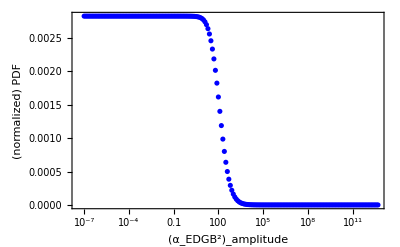

```mathematica
plotαFinalPDFampLogNorm=ListLogLinearPlot[{αFinalPDFampLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_amplitude","(normalized) PDF"}]
```

```mathematica
αFinalPDFampInterpLogNorm=Interpolation[αFinalPDFampLogNorm];
```

```mathematica
αFinalCDFampNorm=Table[{αSampleLogamp[[i]],NIntegrate[αFinalPDFampInterpLogNorm[x],{x,0,αSampleLogamp[[i]]}]},{i,1,Length[αSampleLogamp]}]
```

{{0,0},{1.×10^-7,2.82717×10^-10},{1.25893×10^-7,3.55919×10^-10},{1.58489×10^-7,4.48076×10^-10},{1.99526×10^-7,5.64094×10^-10},{2.51189×10^-7,7.10153×10^-10},{3.16228×10^-7,8.94029×10^-10},{3.98107×10^-7,1.12552×10^-9},{5.01187×10^-7,1.41694×10^-9},{6.30957×10^-7,1.78382×10^-9},{7.94328×10^-7,2.2457×10^-9},{1.×10^-6,2.82717×10^-9},{1.25893×10^-6,3.55919×10^-9},{1.58489×10^-6,4.48076×10^-9},{1.99526×10^-6,5.64094×10^-9},{2.51189×10^-6,7.10153×10^-9},{3.16228×10^-6,8.94029×10^-9},{3.98107×10^-6,1.12552×10^-8},{5.01187×10^-6,1.41694×10^-8},{6.30957×10^-6,1.78382×10^-8},{7.94328×10^-6,2.2457×10^-8},{0.00001,2.82717×10^-8},{0.0000125893,3.55919×10^-8},{0.0000158489,4.48076×10^-8},{0.0000199526,5.64094×10^-8},{0.0000251189,7.10153×10^-8},{0.0000316228,8.94029×10^-8},{0.0000398107,1.12552×10^-7},{0.0000501187,1.41694×10^-7},{0.0000630957,1.78382×10^-7},{0.0000794328,2.2457×10^-7},{0.0001,2.82717×10^-7},{0.000125893,3.55919×10^-7},{0.000158489,4.48076×10^-7},{0.000199526,5.64094×10^-7},{0.000251189,7.10153×10^-7},{0.000316228,8.94029×10^-7},{0.000398107,1.12552×10^-6},{0.000501187,1.41694×10^-6},{0.000630957,1.78382×10^-6},{0.000794328,2.2457×10^-6},{0.001,2.82717×10^-6},{0.00125893,3.55919×10^-6},{0.00158489,4.48076×10^-6},{0.00199526,5.64094×10^-6},{0.00251189,7.10153×10^-6},{0.00316228,8.94029×10^-6},{0.00398107,0.0000112552},{0.00501187,0.0000141694},{0.00630957,0.0000178382},{0.00794328,0.000022457},{0.01,0.0000282717},{0.0125893,0.0000355919},{0.0158489,0.0000448076},{0.0199526,0.0000564094},{0.0251189,0.0000710153},{0.0316228,0.0000894029},{0.0398107,0.000112552},{0.0501187,0.000141694},{0.0630957,0.000178382},{0.0794328,0.00022457},{0.1,0.000282717},{0.125893,0.000355919},{0.158489,0.000448075},{0.199526,0.000564093},{0.251189,0.00071015},{0.316228,0.000894023},{0.398107,0.0011255},{0.501187,0.00141692},{0.630957,0.00178377},{0.794328,0.0022456},{1.,0.00282697},{1.25893,0.0035588},{1.58489,0.00447997},{1.99526,0.00563936},{2.51189,0.00709838},{3.16228,0.00893402},{3.98107,0.0112427},{5.01187,0.0141446},{6.30957,0.017789},{7.94328,0.0223597},{10.,0.0280805},{12.5893,0.035219},{15.8489,0.0440882},{19.9526,0.0550437},{25.1189,0.068475},{31.6228,0.0847929},{39.8107,0.104409},{50.1187,0.127698},{63.0957,0.154946},{79.4328,0.186277},{100.,0.221597},{125.893,0.260564},{158.489,0.302615},{199.526,0.347008},{251.189,0.39289},{316.228,0.439368},{398.107,0.485589},{501.187,0.530793},{630.957,0.574338},{794.328,0.615705},{1000.,0.654502},{1258.93,0.690475},{1584.89,0.723494},{1995.26,0.753527},{2511.89,0.780621},{3162.28,0.804891},{3981.07,0.826505},{5011.87,0.845665},{6309.57,0.862603},{7943.28,0.877578},{10000.,0.890854},{12589.3,0.902667},{15848.9,0.913211},{19952.6,0.922639},{25118.9,0.931074},{31622.8,0.938613},{39810.7,0.945344},{50118.7,0.951347},{63095.7,0.956705},{79432.8,0.961489},{100000.,0.965758},{125893.,0.969561},{158489.,0.972947},{199526.,0.975957},{251189.,0.978628},{316228.,0.980987},{398107.,0.983067},{501187.,0.9849},{630957.,0.986517},{794328.,0.987946},{1.×10^6,0.989213},{1.25893×10^6,0.990338},{1.58489×10^6,0.991337},{1.99526×10^6,0.992222},{2.51189×10^6,0.993005},{3.16228×10^6,0.993702},{3.98107×10^6,0.994327},{5.01187×10^6,0.994892},{6.30957×10^6,0.995406},{7.94328×10^6,0.995878},{1.×10^7,0.996313},{1.25893×10^7,0.996714},{1.58489×10^7,0.997082},{1.99526×10^7,0.997417},{2.51189×10^7,0.997716},{3.16228×10^7,0.997979},{3.98107×10^7,0.998207},{5.01187×10^7,0.998402},{6.30957×10^7,0.998569},{7.94328×10^7,0.99871},{1.×10^8,0.998831},{1.25893×10^8,0.998936},{1.58489×10^8,0.999029},{1.99526×10^8,0.999115},{2.51189×10^8,0.999198},{3.16228×10^8,0.999279},{3.98107×10^8,0.999357},{5.01187×10^8,0.999432},{6.30957×10^8,0.9995},{7.94328×10^8,0.99956},{1.×10^9,0.999611},{1.25893×10^9,0.999654},{1.58489×10^9,0.999689},{1.99526×10^9,0.99972},{2.51189×10^9,0.999748},{3.16228×10^9,0.999774},{3.98107×10^9,0.999797},{5.01187×10^9,0.999819},{6.30957×10^9,0.99984},{7.94328×10^9,0.999859},{1.×10^10,0.999876},{1.25893×10^10,0.999892},{1.58489×10^10,0.999905},{1.99526×10^10,0.999918},{2.51189×10^10,0.99993},{3.16228×10^10,0.999942},{3.98107×10^10,0.999954},{5.01187×10^10,0.999964},{6.30957×10^10,0.999974},{7.94328×10^10,0.999981},{1.×10^11,0.999988},{1.25893×10^11,0.999993},{1.58489×10^11,0.999996},{1.99526×10^11,0.999998},{2.51189×10^11,0.999999},{3.16228×10^11,1.},{3.98107×10^11,1.},{5.01187×10^11,1.},{6.30957×10^11,1.},{7.94328×10^11,1.},{1.×10^12,1.},{1.25893×10^12,1.},{1.58489×10^12,1.},{1.99526×10^12,1.},{2.51189×10^12,1.},{3.16228×10^12,1.},{3.98107×10^12,1.},{5.01187×10^12,1.}}

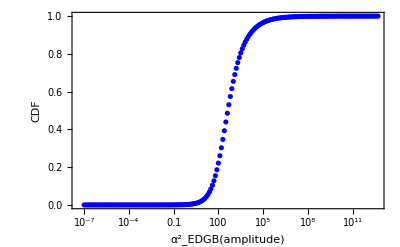

```mathematica
ListLogLinearPlot[αFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB(amplitude)","CDF"}]
```

```mathematica
αFinalCDFampNormInterp=Interpolation[αFinalCDFampNorm];
```

```mathematica
αSquared90CLamp=x/.FindRoot[αFinalCDFampNormInterp[x]==0.9,{x,1000}](*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

11915.1

```mathematica
√√αSquared90CLamp
```

10.4478

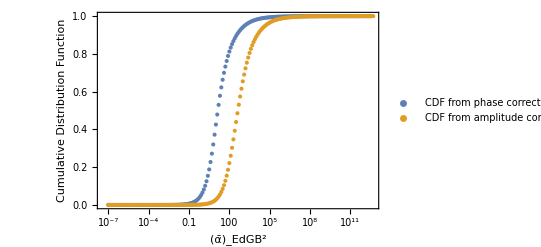

```mathematica
PlotCDFComparison=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm},PlotRange->All,TicksStyle->Directive["Label",14],AxesLabel->{nPN,Subscript[σ, α]},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction"},LabelStyle->{FontSize->5},LegendMarkerSize->10,LegendMargins->0,LegendFunction->"Frame"],{Left,Top}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},Frame->True] (*Shows that indeed for GW150914, the amplitude and phase corrections are comparable*)
```

Combined Correction

```mathematica
LogSquaredαcomb=Log[SqrtαEDGBcomb^4] (*This is Log of sigma_(alpha^2)*)
```

{2.58622,6.60378,3.20885,4.35259,6.27999,3.1092,2.20243,3.99285,2.43945,52234,8.06368,2.47376,3.14189,2.83681,0.701757,3.01884,5.90746,2.88586,3.60932}
 |  |  |  |

```mathematica
MaxLogSquaredαcomb=Max[LogSquaredαcomb]
```

25.6803

```mathematica
MinLogSquaredαcomb=Min[LogSquaredαcomb]
```

-0.474639

```mathematica
𝒟logαcomb=HistogramDistribution[LogSquaredαcomb] ;
```

```mathematica
pslogαcomb=PDF[𝒟logαcomb,x];
```

```mathematica
Histogram[LogSquaredαcomb];
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLogcomb=Prepend[10^Range[-7,12.5,0.1],0];(*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

```mathematica
fun1αcombTable[y_]=Table[{αSampleLogcomb[[i]],fun1αphase[αSampleLogcomb[[i]],y]},{i,1,Length[αSampleLogcomb]}];
```

```mathematica
(*αcombMC[x_]=pslogαcomb;*)
```

```mathematica
𝒟logαSqcomb=SmoothKernelDistribution[LogSquaredαcomb]
```

DataDistribution[…]

```mathematica
𝒟logαSqcomb2=PDF[𝒟logαSqcomb,x]
```

Piecewise[{{InterpolatingFunction[…][x], -1.33308≤x≤26.5387}, {0, True}}]

```mathematica
𝒟logαSqcomb3[x_]=𝒟logαSqcomb2
```

Piecewise[{{InterpolatingFunction[…][x], -1.33308≤x≤26.5387}, {0, True}}]

```mathematica
(*Plot[𝒟logαSqcomb3[x],{x,4,37},PlotRange->All]*)
```

```mathematica
(*αcombMC[8]*)
```

```mathematica
(*αcombMC[32]*)
```

```mathematica
(*αMCSample=Range[7,32,1]*)
```

```mathematica
(*αMCTablecomb=Table[{αMCSample[[i]],αcombMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];*)
```

```mathematica
(*αMCTableInterpcomb=Interpolation[αMCTablecomb];*)
```

```mathematica
(*plotαMCTableInterpcomb=Plot[αMCTableInterpcomb[x],{x,5,37},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]*)
```

```mathematica
(*plot8=Plot[αcombMC[x],{x,5,37},Filling->Axis,PlotStyle->Gray,PlotRange->All]*)
```

```mathematica
(*Show[plot8,plotαMCTableInterpcomb] (*Interpolation matches the actual pdf of monte-carlo*)*)
```

```mathematica
αFinalPDFcombLog=Table[{fun1αcombTable[y][[i,1]],NIntegrate[fun1αcombTable[y][[i,2]]*𝒟logαSqcomb3[y],{y,MinLogSquaredαcomb,MaxLogSquaredαcomb}]},{i,1,Length[fun1αcombTable[y]]}]
```

{{0,0.0331793},{1.×10^-7,0.0331793},{1.25893×10^-7,0.0331793},{1.58489×10^-7,0.0331793},{1.99526×10^-7,0.0331793},{2.51189×10^-7,0.0331793},{3.16228×10^-7,0.0331793},{3.98107×10^-7,0.0331793},{5.01187×10^-7,0.0331793},{6.30957×10^-7,0.0331793},{7.94328×10^-7,0.0331793},{1.×10^-6,0.0331793},{1.25893×10^-6,0.0331793},{1.58489×10^-6,0.0331793},{1.99526×10^-6,0.0331793},{2.51189×10^-6,0.0331793},{3.16228×10^-6,0.0331793},{3.98107×10^-6,0.0331793},{5.01187×10^-6,0.0331793},{6.30957×10^-6,0.0331793},{7.94328×10^-6,0.0331793},{0.00001,0.0331793},{0.0000125893,0.0331793},{0.0000158489,0.0331793},{0.0000199526,0.0331793},{0.0000251189,0.0331793},{0.0000316228,0.0331793},{0.0000398107,0.0331793},{0.0000501187,0.0331793},{0.0000630957,0.0331793},{0.0000794328,0.0331793},{0.0001,0.0331793},{0.000125893,0.0331793},{0.000158489,0.0331793},{0.000199526,0.0331793},{0.000251189,0.0331793},{0.000316228,0.0331793},{0.000398107,0.0331793},{0.000501187,0.0331793},{0.000630957,0.0331793},{0.000794328,0.0331793},{0.001,0.0331793},{0.00125893,0.0331793},{0.00158489,0.0331793},{0.00199526,0.0331793},{0.00251189,0.0331793},{0.00316228,0.0331793},{0.00398107,0.0331793},{0.00501187,0.0331793},{0.00630957,0.0331792},{0.00794328,0.0331792},{0.01,0.0331791},{0.0125893,0.033179},{0.0158489,0.0331789},{0.0199526,0.0331786},{0.0251189,0.0331782},{0.0316228,0.0331775},{0.0398107,0.0331765},{0.0501187,0.0331748},{0.0630957,0.0331722},{0.0794328,0.033168},{0.1,0.0331615},{0.125893,0.033151},{0.158489,0.0331346},{0.199526,0.0331086},{0.251189,0.0330677},{0.316228,0.0330034},{0.398107,0.0329031},{0.501187,0.032748},{0.630957,0.0325109},{0.794328,0.0321557},{1.,0.0316371},{1.25893,0.030906},{1.58489,0.0299167},{1.99526,0.0286331},{2.51189,0.027028},{3.16228,0.0250822},{3.98107,0.0227931},{5.01187,0.0201944},{6.30957,0.0173713},{7.94328,0.0144596},{10.,0.0116265},{12.5893,0.00903917},{15.8489,0.00682536},{19.9526,0.00504142},{25.1189,0.00367019},{31.6228,0.00264855},{39.8107,0.00190055},{50.1187,0.00135751},{63.0957,0.00096514},{79.4328,0.00068311},{100.,0.000481585},{125.893,0.000338359},{158.489,0.000237211},{199.526,0.000166358},{251.189,0.000117031},{316.228,0.0000826713},{398.107,0.0000585911},{501.187,0.0000416033},{630.957,0.0000295573},{794.328,0.0000209847},{1000.,0.0000148784},{1258.93,0.000010541},{1584.89,7.47228×10^-6},{1995.26,5.30036×10^-6},{2511.89,3.75675×10^-6},{3162.28,2.65902×10^-6},{3981.07,1.88091×10^-6},{5011.87,1.32951×10^-6},{6309.57,9.37413×10^-7},{7943.28,6.58394×10^-7},{10000.,4.6091×10^-7},{12589.3,3.22358×10^-7},{15848.9,2.25806×10^-7},{19952.6,1.58547×10^-7},{25118.9,1.11568×10^-7},{31622.8,7.86933×10^-8},{39810.7,5.55432×10^-8},{50118.7,3.91151×10^-8},{63095.7,2.75041×10^-8},{79432.8,1.94118×10^-8},{100000.,1.3811×10^-8},{125893.,9.90634×10^-9},{158489.,7.157×10^-9},{199526.,5.20899×10^-9},{251189.,3.81269×10^-9},{316228.,2.79457×10^-9},{398107.,2.04043×10^-9},{501187.,1.47466×10^-9},{630957.,1.04903×10^-9},{794328.,7.33253×10^-10},{1.×10^6,5.04844×10^-10},{1.25893×10^6,3.43907×10^-10},{1.58489×10^6,2.32921×10^-10},{1.99526×10^6,1.5768×10^-10},{2.51189×10^6,1.07169×10^-10},{3.16228×10^6,7.34863×10^-11},{3.98107×10^6,5.15403×10^-11},{5.01187×10^6,3.76606×10^-11},{6.30957×10^6,2.86637×10^-11},{7.94328×10^6,2.22344×10^-11},{1.×10^7,1.71804×10^-11},{1.25893×10^7,1.30134×10^-11},{1.58489×10^7,9.53833×10^-12},{1.99526×10^7,6.7089×10^-12},{2.51189×10^7,4.53458×10^-12},{3.16228×10^7,2.99302×10^-12},{3.98107×10^7,1.99031×10^-12},{5.01187×10^7,1.37029×10^-12},{6.30957×10^7,9.75505×10^-13},{7.94328×10^7,7.0613×10^-13},{1.×10^8,5.17156×10^-13},{1.25893×10^8,3.83864×10^-13},{1.58489×10^8,2.86691×10^-13},{1.99526×10^8,2.11712×10^-13},{2.51189×10^8,1.52605×10^-13},{3.16228×10^8,1.08377×10^-13},{3.98107×10^8,7.7872×10^-14},{5.01187×10^8,5.76669×10^-14},{6.30957×10^8,4.40433×10^-14},{7.94328×10^8,3.43381×10^-14},{1.×10^9,2.67072×10^-14},{1.25893×10^9,2.01322×10^-14},{1.58489×10^9,1.4512×10^-14},{1.99526×10^9,1.01566×10^-14},{2.51189×10^9,7.0783×10^-15},{3.16228×10^9,4.90641×10^-15},{3.98107×10^9,3.31178×10^-15},{5.01187×10^9,2.18088×10^-15},{6.30957×10^9,1.46455×10^-15},{7.94328×10^9,1.05959×10^-15},{1.×10^10,8.43623×10^-16},{1.25893×10^10,7.23846×10^-16},{1.58489×10^10,6.33573×10^-16},{1.99526×10^10,5.35747×10^-16},{2.51189×10^10,4.24064×10^-16},{3.16228×10^10,3.10553×10^-16},{3.98107×10^10,2.13258×10^-16},{5.01187×10^10,1.44505×10^-16},{6.30957×10^10,1.03908×10^-16},{7.94328×10^10,8.1565×10^-17},{1.×10^11,6.61364×10^-17},{1.25893×10^11,5.0805×10^-17},{1.58489×10^11,3.44093×10^-17},{1.99526×10^11,1.91971×10^-17},{2.51189×10^11,8.09866×10^-18},{3.16228×10^11,2.28978×10^-18},{3.98107×10^11,3.61267×10^-19},{5.01187×10^11,2.36922×10^-20},{6.30957×10^11,3.99381×10^-22},{7.94328×10^11,7.96667×10^-25},{1.×10^12,5.4498×10^-29},{1.25893×10^12,1.78633×10^-35},{1.58489×10^12,1.2363×10^-45},{1.99526×10^12,1.28053×10^-61},{2.51189×10^12,7.7783×10^-87},{3.16228×10^12,1.10399×10^-126}}

```mathematica
αFinalPDFcombInterpLog=Interpolation[αFinalPDFcombLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationcomb=NIntegrate[αFinalPDFcombInterpLog[x],{x,0,3.16227*10^15}]
```

InterpolatingFunction::dmvali: The integration endpoint 3.16227×10^15 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.499439

```mathematica
αFinalPDFcombLogNorm=Table[{αFinalPDFcombLog[[i,1]],αFinalPDFcombLog[[i,2]]/αNormalizationcomb},{i,1,Length[αFinalPDFcombLog]}]
```

{{0,0.0664331},{1.×10^-7,0.0664331},{1.25893×10^-7,0.0664331},{1.58489×10^-7,0.0664331},{1.99526×10^-7,0.0664331},{2.51189×10^-7,0.0664331},{3.16228×10^-7,0.0664331},{3.98107×10^-7,0.0664331},{5.01187×10^-7,0.0664331},{6.30957×10^-7,0.0664331},{7.94328×10^-7,0.0664331},{1.×10^-6,0.0664331},{1.25893×10^-6,0.0664331},{1.58489×10^-6,0.0664331},{1.99526×10^-6,0.0664331},{2.51189×10^-6,0.0664331},{3.16228×10^-6,0.0664331},{3.98107×10^-6,0.0664331},{5.01187×10^-6,0.0664331},{6.30957×10^-6,0.0664331},{7.94328×10^-6,0.0664331},{0.00001,0.0664331},{0.0000125893,0.0664331},{0.0000158489,0.0664331},{0.0000199526,0.0664331},{0.0000251189,0.0664331},{0.0000316228,0.0664331},{0.0000398107,0.0664331},{0.0000501187,0.0664331},{0.0000630957,0.0664331},{0.0000794328,0.0664331},{0.0001,0.0664331},{0.000125893,0.0664331},{0.000158489,0.0664331},{0.000199526,0.0664331},{0.000251189,0.0664331},{0.000316228,0.0664331},{0.000398107,0.0664331},{0.000501187,0.0664331},{0.000630957,0.0664331},{0.000794328,0.0664331},{0.001,0.0664331},{0.00125893,0.0664331},{0.00158489,0.0664331},{0.00199526,0.0664331},{0.00251189,0.0664331},{0.00316228,0.0664331},{0.00398107,0.066433},{0.00501187,0.066433},{0.00630957,0.066433},{0.00794328,0.0664329},{0.01,0.0664327},{0.0125893,0.0664325},{0.0158489,0.0664322},{0.0199526,0.0664317},{0.0251189,0.0664308},{0.0316228,0.0664295},{0.0398107,0.0664274},{0.0501187,0.0664241},{0.0630957,0.0664189},{0.0794328,0.0664105},{0.1,0.0663974},{0.125893,0.0663765},{0.158489,0.0663435},{0.199526,0.0662915},{0.251189,0.0662095},{0.316228,0.0660809},{0.398107,0.0658801},{0.501187,0.0655694},{0.630957,0.0650949},{0.794328,0.0643835},{1.,0.0633452},{1.25893,0.0618814},{1.58489,0.0599006},{1.99526,0.0573305},{2.51189,0.0541167},{3.16228,0.0502207},{3.98107,0.0456375},{5.01187,0.0404341},{6.30957,0.0347816},{7.94328,0.0289516},{10.,0.0232791},{12.5893,0.0180986},{15.8489,0.013666},{19.9526,0.0100942},{25.1189,0.00734862},{31.6228,0.00530304},{39.8107,0.00380537},{50.1187,0.00271807},{63.0957,0.00193245},{79.4328,0.00136775},{100.,0.000964251},{125.893,0.000677478},{158.489,0.000474955},{199.526,0.00033309},{251.189,0.000234325},{316.228,0.000165528},{398.107,0.000117314},{501.187,0.0000833},{630.957,0.000059181},{794.328,0.0000420164},{1000.,0.0000297901},{1258.93,0.0000211056},{1584.89,0.0000149613},{1995.26,0.0000106126},{2511.89,7.52194×10^-6},{3162.28,5.32401×10^-6},{3981.07,3.76603×10^-6},{5011.87,2.66201×10^-6},{6309.57,1.87693×10^-6},{7943.28,1.31827×10^-6},{10000.,9.22854×10^-7},{12589.3,6.45439×10^-7},{15848.9,4.5212×10^-7},{19952.6,3.17449×10^-7},{25118.9,2.23387×10^-7},{31622.8,1.57563×10^-7},{39810.7,1.11211×10^-7},{50118.7,7.8318×10^-8},{63095.7,5.50699×10^-8},{79432.8,3.88672×10^-8},{100000.,2.76531×10^-8},{125893.,1.98349×10^-8},{158489.,1.43301×10^-8},{199526.,1.04297×10^-8},{251189.,7.63394×10^-9},{316228.,5.59541×10^-9},{398107.,4.08544×10^-9},{501187.,2.95263×10^-9},{630957.,2.10042×10^-9},{794328.,1.46815×10^-9},{1.×10^6,1.01082×10^-9},{1.25893×10^6,6.88585×10^-10},{1.58489×10^6,4.66366×10^-10},{1.99526×10^6,3.15713×10^-10},{2.51189×10^6,2.1458×10^-10},{3.16228×10^6,1.47138×10^-10},{3.98107×10^6,1.03196×10^-10},{5.01187×10^6,7.54057×10^-11},{6.30957×10^6,5.73917×10^-11},{7.94328×10^6,4.45186×10^-11},{1.×10^7,3.43994×10^-11},{1.25893×10^7,2.60561×10^-11},{1.58489×10^7,1.90981×10^-11},{1.99526×10^7,1.34329×10^-11},{2.51189×10^7,9.07934×10^-12},{3.16228×10^7,5.99276×10^-12},{3.98107×10^7,3.98509×10^-12},{5.01187×10^7,2.74366×10^-12},{6.30957×10^7,1.9532×10^-12},{7.94328×10^7,1.41384×10^-12},{1.×10^8,1.03547×10^-12},{1.25893×10^8,7.68591×10^-13},{1.58489×10^8,5.74026×10^-13},{1.99526×10^8,4.239×10^-13},{2.51189×10^8,3.05552×10^-13},{3.16228×10^8,2.16998×10^-13},{3.98107×10^8,1.55919×10^-13},{5.01187×10^8,1.15463×10^-13},{6.30957×10^8,8.81854×10^-14},{7.94328×10^8,6.87533×10^-14},{1.×10^9,5.34743×10^-14},{1.25893×10^9,4.03096×10^-14},{1.58489×10^9,2.90567×10^-14},{1.99526×10^9,2.0336×10^-14},{2.51189×10^9,1.41725×10^-14},{3.16228×10^9,9.82384×10^-15},{3.98107×10^9,6.63098×10^-15},{5.01187×10^9,4.36665×10^-15},{6.30957×10^9,2.93238×10^-15},{7.94328×10^9,2.12156×10^-15},{1.×10^10,1.68914×10^-15},{1.25893×10^10,1.44932×10^-15},{1.58489×10^10,1.26857×10^-15},{1.99526×10^10,1.0727×10^-15},{2.51189×10^10,8.49079×10^-16},{3.16228×10^10,6.21802×10^-16},{3.98107×10^10,4.26995×10^-16},{5.01187×10^10,2.89334×10^-16},{6.30957×10^10,2.08048×10^-16},{7.94328×10^10,1.63313×10^-16},{1.×10^11,1.32421×10^-16},{1.25893×10^11,1.01724×10^-16},{1.58489×10^11,6.88959×10^-17},{1.99526×10^11,3.84373×10^-17},{2.51189×10^11,1.62155×10^-17},{3.16228×10^11,4.5847×10^-18},{3.98107×10^11,7.23346×10^-19},{5.01187×10^11,4.74376×10^-20},{6.30957×10^11,7.99659×10^-22},{7.94328×10^11,1.59512×10^-24},{1.×10^12,1.09118×10^-28},{1.25893×10^12,3.57666×10^-35},{1.58489×10^12,2.47538×10^-45},{1.99526×10^12,2.56394×10^-61},{2.51189×10^12,1.55741×10^-86},{3.16228×10^12,2.21045×10^-126}}

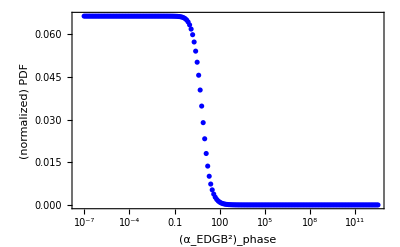

```mathematica
plotαFinalPDFcombLogNorm=ListLogLinearPlot[{αFinalPDFcombLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFcombInterpLogNorm=Interpolation[αFinalPDFcombLogNorm]
```

InterpolatingFunction[…]

```mathematica
αFinalCDFcombNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFcombInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}]
```

{{0,0},{1.×10^-7,6.64331×10^-9},{1.25893×10^-7,8.36343×10^-9},{1.58489×10^-7,1.05289×10^-8},{1.99526×10^-7,1.32551×10^-8},{2.51189×10^-7,1.66872×10^-8},{3.16228×10^-7,2.1008×10^-8},{3.98107×10^-7,2.64475×10^-8},{5.01187×10^-7,3.32954×10^-8},{6.30957×10^-7,4.19165×10^-8},{7.94328×10^-7,5.27697×10^-8},{1.×10^-6,6.64331×10^-8},{1.25893×10^-6,8.36343×10^-8},{1.58489×10^-6,1.05289×10^-7},{1.99526×10^-6,1.32551×10^-7},{2.51189×10^-6,1.66872×10^-7},{3.16228×10^-6,2.1008×10^-7},{3.98107×10^-6,2.64475×10^-7},{5.01187×10^-6,3.32954×10^-7},{6.30957×10^-6,4.19165×10^-7},{7.94328×10^-6,5.27697×10^-7},{0.00001,6.64331×10^-7},{0.0000125893,8.36343×10^-7},{0.0000158489,1.05289×10^-6},{0.0000199526,1.32551×10^-6},{0.0000251189,1.66872×10^-6},{0.0000316228,2.1008×10^-6},{0.0000398107,2.64475×10^-6},{0.0000501187,3.32954×10^-6},{0.0000630957,4.19165×10^-6},{0.0000794328,5.27697×10^-6},{0.0001,6.64331×10^-6},{0.000125893,8.36343×10^-6},{0.000158489,0.0000105289},{0.000199526,0.0000132551},{0.000251189,0.0000166872},{0.000316228,0.000021008},{0.000398107,0.0000264475},{0.000501187,0.0000332954},{0.000630957,0.0000419165},{0.000794328,0.0000527697},{0.001,0.0000664331},{0.00125893,0.0000836343},{0.00158489,0.000105289},{0.00199526,0.000132551},{0.00251189,0.000166872},{0.00316228,0.00021008},{0.00398107,0.000264475},{0.00501187,0.000332954},{0.00630957,0.000419164},{0.00794328,0.000527696},{0.01,0.00066433},{0.0125893,0.000836341},{0.0158489,0.00105289},{0.0199526,0.00132551},{0.0251189,0.00166871},{0.0316228,0.00210076},{0.0398107,0.00264467},{0.0501187,0.00332939},{0.0630957,0.00419135},{0.0794328,0.00527637},{0.1,0.00664212},{0.125893,0.00836105},{0.158489,0.0105242},{0.199526,0.0132457},{0.251189,0.0166684},{0.316228,0.0209706},{0.398107,0.0263734},{0.501187,0.0331488},{0.630957,0.0416279},{0.794328,0.052206},{1.,0.0653434},{1.25893,0.0815587},{1.58489,0.10141},{1.99526,0.125466},{2.51189,0.154251},{3.16228,0.188171},{3.98107,0.227389},{5.01187,0.271696},{6.30957,0.320396},{7.94328,0.372277},{10.,0.425705},{12.5893,0.478868},{15.8489,0.530112},{19.9526,0.578245},{25.1189,0.622636},{31.6228,0.663114},{39.8107,0.699769},{50.1187,0.732801},{63.0957,0.762434},{79.4328,0.788897},{100.,0.812427},{125.893,0.833272},{158.489,0.851687},{199.526,0.867937},{251.189,0.882302},{316.228,0.89505},{398.107,0.906407},{501.187,0.916551},{630.957,0.925624},{794.328,0.933737},{1000.,0.940984},{1258.93,0.947449},{1584.89,0.953216},{1995.26,0.958365},{2511.89,0.962962},{3162.28,0.967061},{3981.07,0.970712},{5011.87,0.973962},{6309.57,0.976851},{7943.28,0.979411},{10000.,0.981671},{12589.3,0.983661},{15848.9,0.985413},{19952.6,0.986961},{25118.9,0.98833},{31622.8,0.989545},{39810.7,0.990624},{50118.7,0.991582},{63095.7,0.992431},{79432.8,0.993183},{100000.,0.993854},{125893.,0.994457},{158489.,0.995004},{199526.,0.995503},{251189.,0.995962},{316228.,0.996385},{398107.,0.996775},{501187.,0.997133},{630957.,0.997455},{794328.,0.997741},{1.×10^6,0.997991},{1.25893×10^6,0.998206},{1.58489×10^6,0.99839},{1.99526×10^6,0.998547},{2.51189×10^6,0.998681},{3.16228×10^6,0.998796},{3.98107×10^6,0.998896},{5.01187×10^6,0.998986},{6.30957×10^6,0.999071},{7.94328×10^6,0.999153},{1.×10^7,0.999233},{1.25893×10^7,0.999311},{1.58489×10^7,0.999383},{1.99526×10^7,0.999449},{2.51189×10^7,0.999506},{3.16228×10^7,0.999554},{3.98107×10^7,0.999594},{5.01187×10^7,0.999628},{6.30957×10^7,0.999657},{7.94328×10^7,0.999684},{1.×10^8,0.999709},{1.25893×10^8,0.999732},{1.58489×10^8,0.999754},{1.99526×10^8,0.999774},{2.51189×10^8,0.999792},{3.16228×10^8,0.999809},{3.98107×10^8,0.999824},{5.01187×10^8,0.999838},{6.30957×10^8,0.999851},{7.94328×10^8,0.999863},{1.×10^9,0.999876},{1.25893×10^9,0.999888},{1.58489×10^9,0.999899},{1.99526×10^9,0.999909},{2.51189×10^9,0.999918},{3.16228×10^9,0.999925},{3.98107×10^9,0.999932},{5.01187×10^9,0.999938},{6.30957×10^9,0.999942},{7.94328×10^9,0.999946},{1.×10^10,0.99995},{1.25893×10^10,0.999954},{1.58489×10^10,0.999958},{1.99526×10^10,0.999963},{2.51189×10^10,0.999968},{3.16228×10^10,0.999973},{3.98107×10^10,0.999977},{5.01187×10^10,0.999981},{6.30957×10^10,0.999984},{7.94328×10^10,0.999987},{1.×10^11,0.99999},{1.25893×10^11,0.999993},{1.58489×10^11,0.999996},{1.99526×10^11,0.999998},{2.51189×10^11,0.999999},{3.16228×10^11,1.},{3.98107×10^11,1.},{5.01187×10^11,1.},{6.30957×10^11,1.},{7.94328×10^11,1.},{1.×10^12,1.},{1.25893×10^12,1.},{1.58489×10^12,1.},{1.99526×10^12,1.},{2.51189×10^12,1.},{3.16228×10^12,1.}}

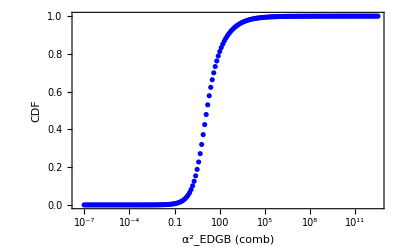

```mathematica
ListLogLinearPlot[αFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (comb)","CDF"}]
```

```mathematica
αFinalCDFcombNormInterp=Interpolation[αFinalCDFcombNorm]
```

InterpolatingFunction[…]

```mathematica
αSquared90CLcomb=x/.FindRoot[αFinalCDFcombNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

348.198

```mathematica
√√αSquared90CLcomb//N
```

4.31973

## Small Coupling Approximation

```mathematica
ζphaseAll2=ζphaseAll*1.64485 (*multiplying with 1.64485 since I want to know how much of the data satisfy small coupling with 90% CL*)
```

{0.000865866,0.0760954,0.00245305,0.00776821,0.0518608,0.00178136,0.000678991,0.00326098,52236,0.000978424,0.00104161,0.00132056,0.0000446668,0.00187482,0.0344808,0.00149917,0.00318839}
 |  |  |  |

```mathematica
Max[ζphaseAll2]
```

1.2923×10^7

```mathematica
ζampAll2=ζampAll*1.64485
```

{0.0282472,2.60782,0.0858722,0.27229,1.79617,0.0622306,0.0210279,0.0878202,0.0274975,52234,9.50206,0.0323325,0.0231492,0.0380406,0.000844861,0.0615145,1.19635,0.0519393,0.112849}
 |  |  |  |

```mathematica
ζcomball2=ζcombAll*1.64485
```

{0.000864957,0.0761268,0.00245167,0.00776728,0.0518813,0.0017805,0.000678225,0.00325808,52236,0.000977441,0.00104198,0.00131916,0.000044739,0.00187293,0.0344929,0.00149821,0.00318787}
 |  |  |  |

Phase:

```mathematica
𝒟logζphase=HistogramDistribution[Log[ζphaseAll2]]
```

DataDistribution[…]

```mathematica
ps1=PDF[𝒟logζphase,x];
```

```mathematica
ps2[x]=ps1;
```

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll2]],Log[Max[ζphaseAll2]]}]
```

0.999954

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll2]],0}]/Integrate[ps2[x],{x,Log[Min[ζphaseAll2]],Log[Max[ζphaseAll2]]}]*100 (*71% area under the curve satisfies zeta<1 from phase correction*)
```

97.7823

```mathematica
Amplitude
```

Amplitude

```mathematica
𝒟logζamp=HistogramDistribution[Log[ζampAll2]]
```

DataDistribution[…]

```mathematica
ps1amp=PDF[𝒟logζamp,x];
```

```mathematica
ps2amp[x]=ps1amp;
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll2]],0}]/Integrate[ps2amp[x],{x,Log[Min[ζampAll2]],Log[Max[ζampAll2]]}]*100
```

86.9452

```mathematica
Combined
```

Combined

```mathematica
𝒟logζcomb=HistogramDistribution[Log[ζcomball2]]
```

DataDistribution[…]

```mathematica
ps1comb=PDF[𝒟logζcomb,x];
```

```mathematica
ps2comb[x]=ps1comb;
```

```mathematica
Integrate[ps2comb[x],{x,Log[Min[ζcomball2]],0}]/Integrate[ps2comb[x],{x,Log[Min[ζcomball2]],Log[Max[ζcomball2]]}]*100
```

97.7823

## Exporting data for xmgrace

```mathematica
Export[NotebookDirectory[]<>"cdfphase.dat",αFinalCDFPhaseNorm]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/cdfphase.dat

```mathematica
Export[NotebookDirectory[]<>"cdfamp.dat",αFinalCDFampNorm]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/cdfamp.dat

```mathematica
Export[NotebookDirectory[]<>"cdfcomb.dat",αFinalCDFcombNorm]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/cdfcomb.dat

```mathematica
{bins,counts}=HistogramList[Log[ζphaseAll2],{0.5}]
```

{{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5},{11,103,485,1098,1550,2000,2016,1744,1504,1184,975,758,625,537,360,304,253,178,161,114,86,55,59,37,26,20,16,15,9,14,9,7,2,2,4,4,1,3,0,1,0,0,0,1,0,0,1}}

```mathematica
Table[Append[{bins[[i]]},counts[[i]]],{i,1,Length[counts]}]
```

{{-5.,11},{-4.5,103},{-4.,485},{-3.5,1098},{-3.,1550},{-2.5,2000},{-2.,2016},{-1.5,1744},{-1.,1504},{-0.5,1184},{0.,975},{0.5,758},{1.,625},{1.5,537},{2.,360},{2.5,304},{3.,253},{3.5,178},{4.,161},{4.5,114},{5.,86},{5.5,55},{6.,59},{6.5,37},{7.,26},{7.5,20},{8.,16},{8.5,15},{9.,9},{9.5,14},{10.,9},{10.5,7},{11.,2},{11.5,2},{12.,4},{12.5,4},{13.,1},{13.5,3},{14.,0},{14.5,1},{15.,0},{15.5,0},{16.,0},{16.5,1},{17.,0},{17.5,0},{18.,1}}

```mathematica
{binsamp,countsamp}=HistogramList[Log[ζampAll2],{0.5}]
```

{{-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.},{1,14,114,446,963,1403,1864,1964,1774,1550,1263,1051,809,671,565,402,311,254,219,158,129,100,65,57,41,28,21,16,18,10,13,11,4,4,3,4,3,2,4,0,1,0,0,0,0,1,0,1}}

```mathematica
Table[Append[{binsamp[[i]]},countsamp[[i]]],{i,1,Length[countsamp]}]
```

{{-4.,1},{-3.5,14},{-3.,114},{-2.5,446},{-2.,963},{-1.5,1403},{-1.,1864},{-0.5,1964},{0.,1774},{0.5,1550},{1.,1263},{1.5,1051},{2.,809},{2.5,671},{3.,565},{3.5,402},{4.,311},{4.5,254},{5.,219},{5.5,158},{6.,129},{6.5,100},{7.,65},{7.5,57},{8.,41},{8.5,28},{9.,21},{9.5,16},{10.,18},{10.5,10},{11.,13},{11.5,11},{12.,4},{12.5,4},{13.,3},{13.5,4},{14.,3},{14.5,2},{15.,4},{15.5,0},{16.,1},{16.5,0},{17.,0},{17.5,0},{18.,0},{18.5,1},{19.,0},{19.5,1}}

```mathematica
{binscomb,countscomb}=HistogramList[Log[ζcomball2],{0.5}]
```

{{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5},{7,78,398,999,1496,1928,2065,1778,1529,1240,1014,792,635,551,390,311,246,203,168,114,95,61,56,37,31,19,14,19,7,16,9,4,4,2,4,4,1,4,0,1,0,0,0,0,1,0,1}}

```mathematica
Table[Append[{binscomb[[i]]},countscomb[[i]]],{i,1,Length[countscomb]}]
```

{{-5.,7},{-4.5,78},{-4.,398},{-3.5,999},{-3.,1496},{-2.5,1928},{-2.,2065},{-1.5,1778},{-1.,1529},{-0.5,1240},{0.,1014},{0.5,792},{1.,635},{1.5,551},{2.,390},{2.5,311},{3.,246},{3.5,203},{4.,168},{4.5,114},{5.,95},{5.5,61},{6.,56},{6.5,37},{7.,31},{7.5,19},{8.,14},{8.5,19},{9.,7},{9.5,16},{10.,9},{10.5,4},{11.,4},{11.5,2},{12.,4},{12.5,4},{13.,1},{13.5,4},{14.,0},{14.5,1},{15.,0},{15.5,0},{16.,0},{16.5,0},{17.,1},{17.5,0},{18.,1}}

```mathematica
Export[NotebookDirectory[]<>"zetaphase.dat",Table[Append[{bins[[i]]},counts[[i]]],{i,1,Length[counts]}]]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/zetaphase.dat

```mathematica
Export[NotebookDirectory[]<>"zetaamp.dat",Table[Append[{binsamp[[i]]},countsamp[[i]]],{i,1,Length[countsamp]}]]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/zetaamp.dat

```mathematica
Export[NotebookDirectory[]<>"zetacomb.dat",Table[Append[{binscomb[[i]]},countscomb[[i]]],{i,1,Length[countscomb]}]]
```

/Users/stshammi/temp/EDGB_bound/EdGB-v2/GW150914/zetacomb.dat

```mathematica
(51.47-50.46)/50.46*100
```

2.00159